# The Music of the (Point-Like) Spheres

## Feynman Diagrams and Music

Silas Kurt Grossberndt

	In the fields of particle physics and music theory, the number 12 is fundamental. For music, there are 12 tones to the chromatic scale (in the western tradition) and, in particle physics, there are 12 fundamental fermions. Particle physics is hard to understand, and often written in the intractable, to the general public, code of Feynman diagrams. Further, physics is often accused of failing to recognize the beauty and art of the world, reducing mystery to mathematical equations. Thus, it would be of interest to represent particle interactions and Feynman diagrams in a musical manner. 

	 However, to just assign random notes to the particles would create a cacophony. To display this issue, let us assign the twelve tones as below

Particle | Tone
up | A
down | B♭
charm | B
strange | C
top | C♯
bottom | D
electron | E♭
muon | E
tau | F
electron neutrino | F♯
muon neutrino | G
tau neutrino | G♯

To test this input, let us consider a basic (non-physical) Feynman diagram

```mathematica
Graph[{1 , 2, 3, 4, 5} ]
```

Graph[{1,2,3,4,5}]

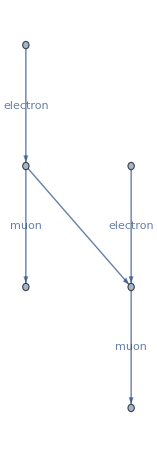

```mathematica
Graph[{Labeled[1->3, "electron"],Labeled[3->2, "muon"],3->4, Labeled[4->5,"muon"] , Labeled[6->4, "electron"]}]
```